```mathematica
d1:=0.3;
d2:=0.1;
m1:=0.25;
```

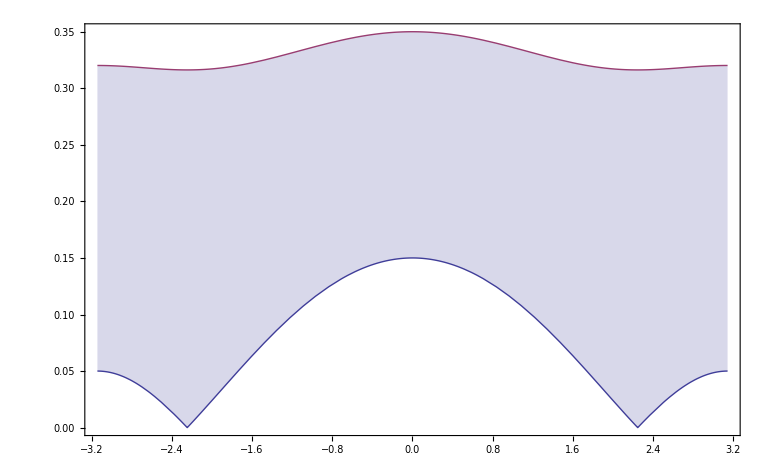

```mathematica
f1[n_,z_]:=√(0.001*n+(m1-√(d1^2+d2^2+2*d1*d2*Cos[z]))^2);
f2[n_,z_]:=-√(0.001*n+(m1-√(d1^2+d2^2+2*d1*d2*Cos[z]))^2);
f3[z_]:=m1-√(d1^2+d2^2-2*d1*d2*Cos[z])
Plot[{f1[0,z],f1[100,z]},{z,-Pi,Pi},Frame->True,Filling->{1->{2}}]
```

```mathematica
f1[1,0]
```

0.153297

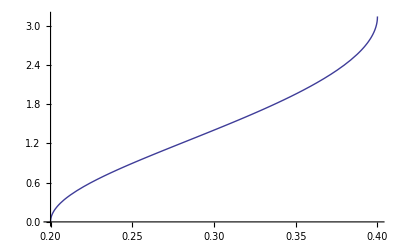

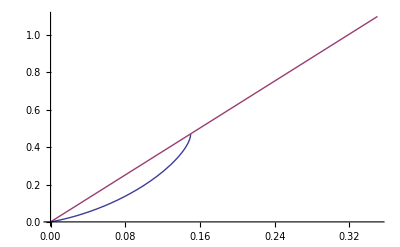

```mathematica
Ro1[en_]:=en*ArcCos[(d1^2+d2^2-(en+m1)^2)/(2*d1*d2)]
f11[x_]:=ArcCos[(d1^2+d2^2-(x)^2)/(2*d1*d2)]
Plot[ArcCos[(d1^2+d2^2-(x)^2)/(2*d1*d2)], {x,d1-d2,d1+d2}]
Plot[{Ro1[en],Pi*en}, {en,0,d1+d2-m1+0.2}]
```

```mathematica
Ro[d1+d2-m1]
```

0.235754

```mathematica
0.2357544490374595
Pi*(d1+d2-m1)
```

0.235754

0.471239